```mathematica
Clear["`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Tcdata1=3*Import["./mu.dat"];
Tcdata2=Import["./T.dat"];
```

```mathematica
Tcdata=Transpose[{Tcdata1[[All,1]],Tcdata2[[All,1]]}];
```

```mathematica
lendata=Length[Tcdata];
```

```mathematica
Tcdata=Table[{Tcdata[[i,1]],Tcdata[[i,2]]},{i,19}];
```

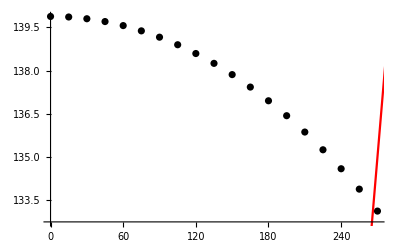

```mathematica
Show[ListPlot[Tcdata,PlotRange->{Automatic, Automatic} ,PlotStyle->Black],Plot[muB/2,{muB,0,500},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]](*Plot[muB/3,{muB,0,500},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]*)
```

```mathematica
muBtoTc=Tcdata;
```

```mathematica
TcPoly[x_]=Fit[muBtoTc, {1,x^2,x^4},x];
```

```mathematica
d2TcR3dT2[muB_]=D[TcPoly[muB],{muB,2}];
```

```mathematica
d2TcR3dT2[0]*TcPoly[0]/(-2)
```

0.0123876